## Auxiliary Functions and Definitions

```mathematica
$Assumptions={_∈Reals, h > 0, Vt > 0, d  > 0, A > 0};

printWithBasis[M_,states_]:=(ML=Length[M];
newM=Table[If[(i==0&&j≠0),states[[j]],If[j==0&&i≠0,states[[i]],If[i==0&&j==0,"",M[[i]][[j]]]]],{i,0,ML},{j,0,ML}];
Print[MatrixForm[newM]])
basisGE = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓>", "|g↑⇑>", "|e↓⇓>", "|e↓⇑>", "|e↑⇓>", "|e↑⇑>"};
basisGERotated = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓> + |e↓⇑>", "|g↑⇑>", "|e↓⇓>", "|g↑⇓> - |e↓⇑>", "|e↑⇓>", "|e↑⇑>"};

TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];

Sx=(hBar/2)σX;
Sy=(hBar/2)σY;
Sz=(hBar/2)σZ;

Ix=(hBar/2)σX;
Iy=(hBar/2)σY;
Iz=(hBar/2)σZ;

SdotI=TProduct[Sx,Ix]+TProduct[Sy,Iy]+TProduct[Sz,Iz];

hBar=1;

transform[M_,U_]:=U.M.ConjugateTranspose[U]-ⅈ*hBar*U.ConjugateTranspose[D[U, t]]

(* SI units *)
setVariables[]:=(
ΔE = 0;
B0 = 0.20112299109490023;(* T *)
d=15*10^-9; (* m *)
A=117*10^6; (* Hz *)
γe=27.97*10^9; (* Hz/T *)
γn=17.23*10^6; (* Hz/T *)
Δγ=-.002;
h=6.62607004*10^-34; (* J*s *)
e=-1.60217662*10^-19; (* C *)
Vt = γe*B0 + A/4; (* Hz *)
δB = γe*B0 - νB;

Tmax = 100*10^-9;

(* PARAMETERS OF HIGH-FIDELITY GATE *)
Eamp[t_] := 222.4901014437078 tanhWindow[t,1/100000000,1/10000000]^2 ;
Bamp[t_] := 0.028851198211908263 tanhWindow[t,1/100000000,1/10000000]^2;
ωE = 3.436149741799419*^10;
ωB = 3.4207449326408493*^10;

)

ϵ0 = √(Vt^2+(d^2 e^2 ΔE^2)/h^2);

clearVariables[]:=Clear[B0,Bac,νB,γe,γn,Δγ,A,Aac,ΔE,Eac,νE,Vt,d,h, e, δB, δE, δ, Eamp, Bamp, ωE, ωB, Tmax, t]
clearVariables[]

tanhWindow[t_?NumericQ, τ_, T_] := Piecewise[{{(Tanh[t/(4τ)] - Tanh[0/(4τ)] - Tanh[(t - T)/(4τ)] + Tanh[-T/(4τ)]), 0 < t < T}}, 0]

energiesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[1]]
energiesInOrder[Ef_, M_] := energiesAt[Ef, M][[order[Ef, M]]]
statesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[2]]
statesInOrder[Ef_, M_] := statesAt[Ef, M][[order[Ef, M]]]

targetStates = IdentityMatrix[8];
order[Ef_, M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef, M]]]}]

simulate[M_] := (
Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->30, MaxSteps->Infinity, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];

pT = Abs[state[[2]]]^2 /. t->Tmax;
Print["Transition probability: " <> ToString[pT]];
state
)

fidelity[M_] := (Tr[M.ConjugateTranspose[M]] + Abs[Tr[M]]^2)/(Length[M] + Length[M]^2)
```

## Define Full Hamiltonian

```mathematica
HorbBase = Vt/2 σX-((e*ΔE*d)/(2h))σZ;
β = (√(1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))/(√2);
α = Sqrt[1 - β^2] // FullSimplify;

M = {{α, β}, {-β, α}};

ConjugateTranspose[M].HorbBase.M // FullSimplify // MatrixForm
Print["M diagonalizes Horb when in the |i>,|d> basis, so it transforms from the |g>,|e> basis to the |i>,|d> basis and M^T does the opposite"]
```

(-(√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h) | 0
0 | (√(h^2 Vt^2+d^2 e^2 ΔE^2))/(2 h))

M diagonalizes Horb when in the |i>,|d> basis, so it transforms from the |g>,|e> basis to the |i>,|d> basis and M^T does the opposite

```mathematica
iState = ConjugateTranspose[M].{1, 0} // FullSimplify;
dState = ConjugateTranspose[M].{0, 1} // FullSimplify;
ii = Outer[Times, iState, iState] // FullSimplify;
id = Outer[Times, iState, dState] // FullSimplify;
di = Outer[Times, dState, iState] // FullSimplify;
dd = Outer[Times, dState, dState] // FullSimplify;

(*   sign of HB0 chosen so that the lowest energy is |↓⇑>   *)
HB0=B0 (-γe*TProduct[(σI+Δγ*dd),Sz, σI]+γn*TProduct[σI,σI, Iz]);
HA=TProduct[A*dd,SdotI];
Horb=TProduct[-((e*(ΔE + Eac)*d)/(2h))*(ii - dd) + (Vt/2)(id + di), σI, σI];
HESR = Bac(γe*TProduct[σI,Sx, σI]-γn*TProduct[σI,σI, Ix]);

H = HB0 + HESR + HA + Horb // FullSimplify;

printWithBasis[H, basisGE]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ-√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | (Bac γe)/2 | 0 | -(Vt (4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
|g↓⇑> | -(Bac γn)/2 | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)-h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (Bac γe)/2 | 0 | (Vt (-4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇓> | (Bac γe)/2 | 1/4 A (1-(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (-A √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 B0 γe √(h^2 Vt^2+d^2 e^2 ΔE^2)+4 B0 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+2 B0 γe √(h^2 Vt^2+d^2 e^2 ΔE^2) Δγ+d e ΔE (A-2 B0 γe Δγ)))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | 0 | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇑> | 0 | (Bac γe)/2 | -(Bac γn)/2 | (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(Vt (4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(Vt (4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2 | (Bac γe)/2 | 0
|e↓⇑> | 0 | (Vt (-4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | -(Bac γn)/2 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)-h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 1/4 A (1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (Bac γe)/2
|e↑⇓> | 0 | -(A h Vt)/(4 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | (Vt (-4 d e Eac+h (A-2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | (Bac γe)/2 | 1/4 A (1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))) | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (-A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(Bac γn)/2
|e↑⇑> | 0 | 0 | 0 | -(Vt (4 d e Eac+h (A+2 B0 γe Δγ)))/(8 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | (Bac γe)/2 | -(Bac γn)/2 | (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ)))))/(8 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

## Define a simplified Hamiltonian and remove all off-diagonal terms that aren’t close to resonance

```mathematica
Hsim = 2*π*H;

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = 0;
Hsim[[p[[2]]]][[p[[1]]]] = 0;
),
{p, {{1, 2}, {2, 3}, {2, 7}, {3, 4}, {5, 6}, {6, 7}, {7, 8}}}
];

Do[(
Hsim[[p[[1]]]][[p[[2]]]] = Hsim[[p[[1]]]][[p[[2]]]] - (Hsim[[p[[1]]]][[p[[2]]]]/.{Eac->0, Bac->0});
Hsim[[p[[2]]]][[p[[1]]]] = Hsim[[p[[2]]]][[p[[1]]]] - (Hsim[[p[[2]]]][[p[[1]]]]/.{Eac->0, Bac->0});
),
{p, {{1, 5}, {2, 6}, {3, 7}, {4, 8}}}
];

printWithBasis[Hsim // FullSimplify, basisGE]

(* set sinusoidal driving fields *)
Eac = Eamp[t]*Cos[ωE*t];
Bac = Bamp[t]*Cos[ωB*t];
HsimMid = Hsim;

setVariables[]
(* adjust B0 *)
B0 = 0.20112299109490023;(* T *)

(* set sinusoidal driving fields *)
Eac = Eamp[Tmax/2]*Cos[ωE*t];
Bac = Bamp[Tmax/2]*Cos[ωB*t];

printWithBasis[Hsim // FullSimplify, basisGE]
clearVariables[]
```

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | (π (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ-√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
|g↓⇑> | 0 | -(π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
|g↑⇓> | Bac π γe | 0 | -(π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|g↑⇑> | 0 | Bac π γe | 0 | (π (-4 h^2 Vt^2-4 d^2 e^2 ΔE (Eac+ΔE)+h (A (-d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (-d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))
|e↓⇓> | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))-2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0
|e↓⇑> | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)-h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe
|e↑⇓> | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (-A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
|e↑⇑> | 0 | 0 | 0 | -(d e Eac π Vt)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | Bac π γe | 0 | (π (4 h^2 Vt^2+4 d^2 e^2 ΔE (Eac+ΔE)+h (A (d e ΔE+√(h^2 Vt^2+d^2 e^2 ΔE^2))+2 B0 (-2 γn √(h^2 Vt^2+d^2 e^2 ΔE^2)+γe (d e ΔE Δγ+√(h^2 Vt^2+d^2 e^2 ΔE^2) (2+Δγ))))))/(4 h √(h^2 Vt^2+d^2 e^2 ΔE^2)))

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -3.53169×10^10 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0 | 0
|g↓⇑> | 0 | -3.55225×10^10 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0
|g↑⇓> | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | -1.90569×10^8 | 0 | 0 | -1.83783×10^8 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0
|g↑⇑> | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | -2.85595×10^7 | 0 | 0 | 0 | -1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t]
|e↓⇓> | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 0 | 0 | 2.12343×10^8 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0
|e↓⇑> | 0 | 1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | -1.83783×10^8 | 0 | 0 | 6.78603×10^6 | 0 | 1.27781×10^9 Cos[3.42074×10^10 t]
|e↑⇓> | 0 | 0 | 1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 3.53387×10^10 | 0
|e↑⇑> | 0 | 0 | 0 | -1.49012×10^-8+1.27781×10^9 Cos[3.43615×10^10 t] | 0 | 1.27781×10^9 Cos[3.42074×10^10 t] | 0 | 3.55007×10^10)

## Apply the RWA manually, replacing cos(ωt) with e^ⅈωt/2 or e^-ⅈωt/2, then change to a rotating frame

```mathematica
Eac = Eamp[t]*Exp[ⅈ*ωE*t]/2;
Bac = Bamp[t]*Exp[ⅈ*ωB*t]/2;
For[i = 1, i ≤ 8, i = i + 1,
For[j = 1, j < i, j = j + 1,
Hsim[[i]][[j]] = Conjugate[Hsim[[j]][[i]] // FullSimplify];
Hsim[[j]][[i]] = Conjugate[Hsim[[i]][[j]] // FullSimplify];
]
];
For[i = 1, i ≤ 8, i = i + 1,
Hsim[[i]][[i]] = (Hsim[[i]][[i]] /. Eamp[t]->0)
];

Urot = MatrixExp[ⅈ*DiagonalMatrix[{0, (ωB - ωE)*t, ωB*t, (2*ωB - ωE)*t, ωE*t, ωB*t, (ωB + ωE)*t, 2*ωB*t}]];
HsimRot = transform[Hsim, Urot];
HsimRot = HsimRot - HsimRot[[1]][[1]]*IdentityMatrix[8];
HsimRot = HsimRot // FullSimplify;

HsimRot // MatrixForm
```

(0 | 0 | 1/2 π γe Bamp[t] | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | -2 B0 π γn+1/2 A π (-1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB+ωE | 0 | 1/2 π γe Bamp[t] | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
1/2 π γe Bamp[t] | 0 | 1/2 A π (-1+(d e ΔE)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))+B0 π γe (2+Δγ-(d e ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB | 0 | 0 | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 1/2 π γe Bamp[t] | 0 | B0 π (-2 γn+γe (2+Δγ-(d e ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))))-2 ωB+ωE | 0 | 0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
-(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (4 h^2 π Vt^2+4 d^2 e^2 π ΔE^2+h (d e π ΔE (A-2 B0 γe Δγ)-2 √(h^2 Vt^2+d^2 e^2 ΔE^2) ωE))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0
0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | -(A h π Vt)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | -(A π)/2+(2 π √(h^2 Vt^2+d^2 e^2 ΔE^2))/h+B0 π (-2 γn-(d e γe ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2)))-ωB | 0 | 1/2 π γe Bamp[t]
0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0 | -(A π)/2+(2 π √(h^2 Vt^2+d^2 e^2 ΔE^2))/h+B0 π γe (2+Δγ)-ωB-ωE | 0
0 | 0 | 0 | -(d e π Vt Eamp[t])/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 1/2 π γe Bamp[t] | 0 | (π (4 h^2 Vt^2+A d e h ΔE+4 d^2 e^2 ΔE^2))/(2 h √(h^2 Vt^2+d^2 e^2 ΔE^2))+B0 π (-2 γn+γe (2+Δγ))-2 ωB)

## Plot the eigenenergies of the final Hamiltonian

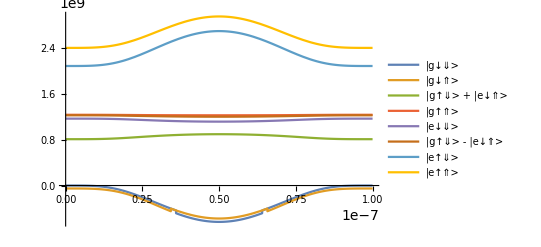

Minimum energy gap between qubit subspace and leakage subspace: 8.08995×10^8

```mathematica
(*setVariables[]

Plot[{
energiesInOrder[0, Hfinal][[1]],
energiesInOrder[0, Hfinal][[2]],
energiesInOrder[0, Hfinal][[3]],
energiesInOrder[0, Hfinal][[4]],
energiesInOrder[0, Hfinal][[5]],
energiesInOrder[0, Hfinal][[6]],
energiesInOrder[0, Hfinal][[7]],
energiesInOrder[0, Hfinal][[8]]
}, {t,0, Tmax}, PlotLegends->basisGERotated]

Print["Minimum energy gap between qubit subspace and leakage subspace: " <> ToString[energiesInOrder[0, Hfinal /. t->0][[3]] - energiesInOrder[0, Hfinal /. t->0][[1]], TraditionalForm]
]

clearVariables[]*)
```

```mathematica
(*setVariables[]

B0 = 0.20112299109490023;(* T *)

eBasis[tt_?NumericQ] := (
spec = Eigensystem[Hfinal /. t->tt][[1]];
eStates = Eigensystem[Hfinal /. t->tt][[2]];
eStates[[Ordering[spec]]]
)

Chop[eBasis[Tmax/2].(Hfinal /. t->Tmax/2).ConjugateTranspose[eBasis[Tmax/2]], 10^-3] // MatrixForm

state = simulate[Hfinal];
stateInEBasis[tt_?NumericQ] := eBasis[tt].(state /. t->tt)

stateInEBasis[0]

LogPlot[{
Max[Abs[stateInEBasis[t][[1]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[2]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[3]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[4]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[5]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[6]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[7]]]^2 // Re, 10^-8],
Max[Abs[stateInEBasis[t][[8]]]^2 // Re, 10^-8]
},{t,0,Tmax}, PlotRange->All, PlotLabel->"Evolution in Eigenbasis"]

clearVariables[]*)
```

## Find Energy Corrections to the RWA

```mathematica
(* Floquet Fourier components *)
HFminus2ωB = IdentityMatrix[8]*0;
HFplus2ωB = IdentityMatrix[8]*0;
HFminus2ωE = IdentityMatrix[8]*0;
HFplus2ωE = IdentityMatrix[8]*0;

dgnl = Diagonal[HsimRot];

Do[
Do[(
If[!FreeQ[HsimRot[[i]][[j]], Bamp[t]],
If[i < j, HFminus2ωB[[i]][[j]] = HsimRot[[i]][[j]], HFplus2ωB[[i]][[j]] = HsimRot[[i]][[j]]];
];
If[!FreeQ[HsimRot[[i]][[j]], Eamp[t]],
If[i < j, HFminus2ωE[[i]][[j]] = HsimRot[[i]][[j]], HFplus2ωE[[i]][[j]] = HsimRot[[i]][[j]]];
];
)
,{j, 1, 8}]
,{i, 1, 8}];

corrections = Table[0, {i, 1, 8}];
Do[
Do[(
If[i ≠ j,
corrections[[i]] = corrections[[i]] + (HFplus2ωB[[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] + 2ωB)) + (HFminus2ωB[[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] - 2ωB)) + (HFplus2ωE[[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] + 2ωE)) + (HFminus2ωE[[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] - 2ωE));
]
)
,{j, 1, 8}]
,{i, 1, 8}];




Clear[correctionMatrix]
correctionMatrix = DiagonalMatrix[corrections];
Hcorrected = HsimRot + correctionMatrix;

setVariables[]
corrections // MatrixForm
clearVariables[]
```

(-4.6164×10^7 tanhWindow[t,1/100000000,1/10000000]^4
-4.60418×10^7 tanhWindow[t,1/100000000,1/10000000]^4
184676. tanhWindow[t,1/100000000,1/10000000]^4
62467.8 tanhWindow[t,1/100000000,1/10000000]^4
-184676. tanhWindow[t,1/100000000,1/10000000]^4
-62467.8 tanhWindow[t,1/100000000,1/10000000]^4
4.6164×10^7 tanhWindow[t,1/100000000,1/10000000]^4
4.60418×10^7 tanhWindow[t,1/100000000,1/10000000]^4)

## Find Energy Corrections a Different Way

```mathematica
dgnl = Diagonal[HsimRot];

dropOscillatingTerms[inputt_] := (
input = inputt + ωB^2 + ωE^2;
output = 0*input;
Do[
(* if a term doesn't depend on either ωE or ωB, keep it *)
If[FreeQ[input[[i]][[j]][[k]], ωE] && FreeQ[input[[i]][[j]][[k]], ωB], output[[i]][[j]] = output[[i]][[j]] + input[[i]][[j]][[k]]]
,{i, 1, 8}, {j, 1, 8}, {k, 1, Length[input[[i]][[j]]]}
];
output
)
HexactRot = transform[Hexact // TrigToExp, Urot] // Simplify // Apart // Expand;

ωs = {-2ωE, -2ωB, 2ωB, 2ωE, -ωE, ωE};
HFs = {};

(* find the Fourier components of the exact Hamiltonian at each frequency *)
Do[
AppendTo[HFs,
dropOscillatingTerms[
Coefficient[HexactRot, E^Expand[ⅈ*ω*t]]
]
]
,{ω, ωs}]

corrections = Table[0, {i, 1, 8}];
Do[
corrections[[i]] = corrections[[i]] + (HFs[[k]][[j]][[i]])^2/(dgnl[[i]] - (dgnl[[j]] + ωs[[k]]));
,{i, 1, 8}, {j, 1, 8}, {k, 1, Length[ωs]}]

correctionMatrix = DiagonalMatrix[corrections];
Hcorrected = HsimRot + correctionMatrix;

setVariables[]
corrections // MatrixForm
clearVariables[]
```

(-337872.-4.6164×10^7 tanhWindow[t,1/100000000,1/10000000]^4
-1.58766×10^6-4.60418×10^7 tanhWindow[t,1/100000000,1/10000000]^4
618098.+184694. tanhWindow[t,1/100000000,1/10000000]^4
-155039.+62467.8 tanhWindow[t,1/100000000,1/10000000]^4
337872.-184659. tanhWindow[t,1/100000000,1/10000000]^4
-800931.-62467.8 tanhWindow[t,1/100000000,1/10000000]^4
1.7705×10^6+4.6164×10^7 tanhWindow[t,1/100000000,1/10000000]^4
155039.+4.60418×10^7 tanhWindow[t,1/100000000,1/10000000]^4)

## Check Fidelity of Approximation

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];findEvolutionOperator[Ham_]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8,8}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]]
)

setVariables[]
B0 = 0.20112299109490023;(* T *)
B0 = .2;

fsCorr = {};

(*Do[
ΔE = eField;*)

Uexact = findEvolutionOperator[Hexact];

(*UwithMissingTerms = findEvolutionOperator[HsimMid];
Mmid = ConjugateTranspose[Uexact].UwithMissingTerms;

UwithRWA = ConjugateTranspose[Urot].findEvolutionOperator[HsimRot];
M = ConjugateTranspose[Uexact].UwithRWA;*)

(*UwithRWACorrected = ConjugateTranspose[Urot].Λ.findEvolutionOperator[Hfinal + correctionMatrix].Λ;*)
UwithRWACorrected = ConjugateTranspose[Urot].findEvolutionOperator[Hcorrected];
Mcorrected = ConjugateTranspose[Uexact].UwithRWACorrected;

Print[{ΔE, fidelity[Mcorrected /. t->Tmax] // Chop}];

(*AppendTo[fsCorr, {ΔE, fidelity[Mcorrected /. t->Tmax]}];*)

(*,{eField, Table[i, {i, -600, -200, 50}]}]*)

(*Plot[{fidelity[Mmid], fidelity[M], fidelity[Mcorrected]}, {t, 0, Tmax}, PlotLegends->{"Without RWA", "With RWA", "With RWA Corrected"}, PlotLabel->"Fidelity"]
Plot[{fidelity[Mmid[[{1, 2}, {1, 2}]]], fidelity[M[[{1, 2}, {1, 2}]]], fidelity[Mcorrected[[{1, 2}, {1, 2}]]]}, {t, 0, Tmax}, PlotLegends->{"Without RWA", "With RWA", "With RWA Corrected"}, PlotLabel->"Fidelity within qubit subspace"]*)


clearVariables[]
```

{0,0.999628}

{{-4000,0.999931},{-3800,0.999932},{-3600,0.999931},{-3400,0.999931},{-3200,0.999931},{-3000,0.999931},{-2800,0.99993},{-2600,0.999509},{-2400,0.99993},{-2200,0.99993},{-2000,0.99993},{-1800,0.999926},{-1600,0.999916},{-1400,0.999902},{-1200,0.99988},{-1000,0.999824},{-800,0.999729},{-600,0.999591},{-400,0.999469},{-200,0.999572},{0,0.999603},{200,0.999603},{400,0.999622},{600,0.999695},{800,0.999781},{1000,0.999849},{1200,0.999888},{1400,0.999907},{1600,0.99992},{1800,0.999925},{2000,0.99993},{2200,0.999932},{2400,0.999931},{2600,0.999508},{2800,0.999931},{3000,0.999932},{3200,0.999931},{3400,0.999931},{3600,0.999931},{3800,0.999931},{4000,0.999931},{-600,0.999591},{-550,0.999554},{-500,0.999524},{-450,0.999495},{-400,0.999469},{-350,0.999474},{-300,0.999496},{-250,0.99954},{-200,0.999572}}

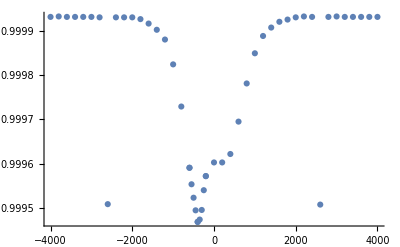

```mathematica
values = {{-4000,0.999931},{-3800,0.999932},{-3600,0.999931},{-3400,0.999931},{-3200,0.999931},{-3000,0.999931},{-2800,0.99993},{-2600,0.999509},{-2400,0.99993},{-2200,0.99993},{-2000,0.99993},{-1800,0.999926},{-1600,0.999916},{-1400,0.999902},{-1200,0.99988},{-1000,0.999824},{-800,0.999729},{-600,0.999591},{-400,0.999469},{-200,0.999572},{0,0.999603},{200,0.999603},{400,0.999622},{600,0.999695},{800,0.999781},{1000,0.999849},{1200,0.999888},{1400,0.999907},{1600,0.99992},{1800,0.999925},{2000,0.99993},{2200,0.999932},{2400,0.999931},{2600,0.999508},{2800,0.999931},{3000,0.999932},{3200,0.999931},{3400,0.999931},{3600,0.999931},{3800,0.999931},{4000,0.999931},{-600,0.9995910286149376},{-550,0.9995538089407685},{-500,0.9995235030001487},{-450,0.9994950791875149},{-400,0.9994689959599571},{-350,0.9994742567385968},{-300,0.9994958902310271},{-250,0.9995404255714077},{-200,0.9995723975013}}
ListPlot[values]
```